```mathematica
(*Surface Charge Distributin*)
(*Load necessary packages*)
<<VectorAnalysis`(*for command of vector analysis*)
<<VectorFieldPlots` (*for drawing field patterns*)
```

```mathematica
(*Define a function which can be used to find electric potential of a single electric charge*)
pot[{Q_,x0_,y0_,z0_}]:=Q/(4π ϵ Sqrt[(x-x0)^2+(y-y0)^2+(z-z0)^2])
(*here x0,y0, z0 are the coordinates of the position of electric charge and x,y,z are the coordinates of any point where electric potential or electric field intensity can be found*)
```

```mathematica
(*no. of charges*)nx=5;xmin=-10;xmax=10;delx=(xmax-xmin)/(nx-1);
ny=5;ymin=-10;ymax=10;dely=(ymax-ymin)/(ny-1);
(*generate the distribution*)
SurfDist=Table[{0.001,xmin+(i-1)*delx,ymin+(j-1)*dely,0},{i,1,nx},{j,1,ny}]
SurfPot=Sum[pot[SurfDist[[i,j]]],{i,1,nx},{j,1,ny}]
SurfPotxy=SurfPot/.{ϵ->1,z->0}
Plot3D[SurfPotxy,{x,-15,15},{y,-15,15},PlotRange->{{-15,15},{-15,15},{0,0.003}},PlotPoints->200]
ContourPlot[SurfPotxy,{x,-11,11},{y,-11,11},PlotRange->{{-11,11},{-11,11}},Contours->20,PlotPoints->50]
```

```mathematica
(*Compute Electric Field Intensity*)
ESurfInt=-Grad[SurfPot,Cartesian[x,y,z]]
MagExy=Norm[ESurfInt]/.{ϵ->1,z->0}
Plot3D[MagExy,{x,-11,11},{y,-11,11},PlotRange->{{-11,11},{-11,11},{0,0.0025}},PlotPoints->100]
(*Plot the components of electric field intensity*)
Plot3D[ESurfInt/.{ϵ->1,z->0},{x,-11,11},{y,-11,11},PlotRange->{{-11,11},{-11,11},{-0.0025,0.0025}},PlotPoints->100]
(*Draw a vector v=2i+3j*)
```

```mathematica
VectorFieldPlot[{ESurfInt[[1]],ESurfInt[[2]]}/.{ϵ->1,z->0},{x,-11,11,0.33},{y,-11,11,0.33},ScaleFactor->1,MaxArrowLength->2]
VectorFieldPlot3D[ESurfInt/.ϵ->1,{x,-11,11,0.31},{y,-11,11,0.31},{z,-2,2,0.91},ScaleFactor->1,MaxArrowLength->2,VectorHeads->True]
```

```mathematica
(*Problem Questions' Types*)
(*
(i)Conversion of given coordinates from one coordinate system to other coordinate system
(ii) Uses of the commands of VectorAnalysis Package, mainly Grad, Div, Curl and Laplacian, on different scalar and vector functions, in different coordinate systems
(iii) Computing field potential, intensity and their plotting in different ways
*)
```

```mathematica
(*Compute the gradient of the following scalar functions f(r,θ,ϕ)=θ^2/r^2+ϕ^3*r^5, v(r)=q/(4 π ϵ r)*)
f[r_,θ_,ϕ_]:=θ^2/r^2+ϕ^3*r^5
gradAns=Grad[f[r,θ,ϕ],Spherical[r,θ,ϕ]]
```

{-(2 θ^2)/r^3+5 r^4 ϕ^3,(2 θ)/r^3,3 r^4 ϕ^2 Csc[θ]}

{0.0000795775/(r^2 ϵ),0,0}

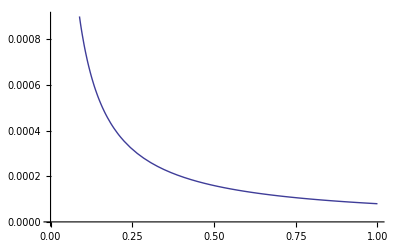

7.95775×10^-6

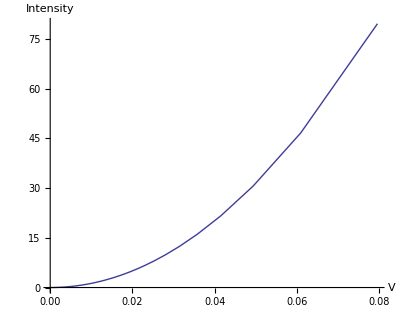

```mathematica
v[Q_,r_]:=Q/(4 π ϵ r)
EInt=-Grad[v[0.001,r],Spherical[r,θ,ϕ]]
Plot[v[0.001,r]/.ϵ->1,{r,0.001,1},PlotRange->{{0,1},{0,0.0009}}]

vvalue=v[0.001,r]/.{ϵ->1,r->10}
ParametricPlot[{v[0.001,r]/.ϵ->1,Norm[EInt/.ϵ->1]},{r,0.001,1},PlotRange->All,AspectRatio->0.8,AxesLabel->{"V","Intensity"}]
```

```mathematica
SphericalPlot3D[{1,1.5,1.7,2},{θ,0,Pi/2},{ϕ,0,2Pi}]
```

```mathematica
??ParametricPlot
```

ParametricPlot[{f_x,f_y},{u,u_min,u_max}] generates a parametric plot of a curve with x and y coordinates f_x and f_y as a function of u. 
ParametricPlot[{{f_x,f_y},{g_x,g_y},…},{u,u_min,u_max}] plots several parametric curves. 
ParametricPlot[{f_x,f_y},{u,u_min,u_max},{v,v_min,v_max}] plots a parametric region. 
ParametricPlot[{{f_x,f_y},{g_x,g_y},…},{u,u_min,u_max},{v,v_min,v_max}] plots several parametric regions.